```mathematica
SOIL=Import["/users/pp/Desktop/soi_loess.txt", "table"];
SOI=Import["/users/pp/Desktop/soi.txt", "table"];
SOICE=Import["/users/pp/Desktop/soi_ce.txt", "table"];
NINO3=Import["/users/pp/Desktop/nino3.txt", "table"];
NINO3a=Import["/users/pp/Desktop/nino3a.txt", "table"];
NINO3s=Import["/users/pp/Desktop/nino3short.txt", "table"];
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
TSID=Import["/users/pp/Desktop/tsi.txt", "table"];
QBO=Import["/users/pp/Desktop/qbo.txt", "table"];  (* qbo20 *)
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
CW=Import["/users/pp/Desktop/cw.txt", "table"];
CW1=Import["/users/pp/Desktop/cw1_1930.txt", "table"];
CW0=Import["/users/pp/Desktop/cw1.txt", "table"];
NINO34=Import["/users/pp/Desktop/nino34ke.txt", "table"];
HC=Import["/users/pp/Desktop/hadcrut4.txt", "table"];
NOAA=Import["/users/pp/Desktop/noaa.txt", "table"];
COWTAN=Import["/users/pp/Desktop/cowtan.txt", "table"];
UEP=Import["/users/pp/Desktop/uep.txt", "table"];
```

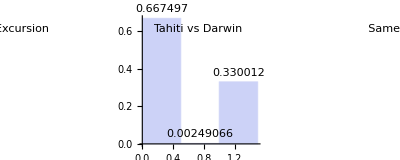

-54.6301

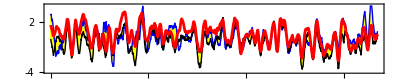

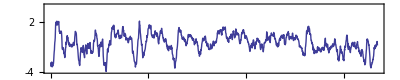

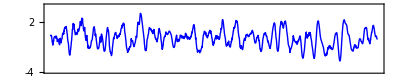

```mathematica
WinHiFilter = 8; WinLowFilter = 450;
TF = MeanFilter[tahiti[[All,2]],WinHiFilter]*2 - 0*MeanFilter[tahiti[[All,2]],WinLowFilter]*2;
DF = -MeanFilter[darwin[[All,2]],WinHiFilter]*2 + 0*MeanFilter[darwin[[All,2]],WinLowFilter]*2; 
R = -2*MeanFilter[NINO34[[All,2]],WinHiFilter] + 0*MeanFilter[NINO34[[All,2]],WinLoFilter]; 
SBIN = Abs[Sign[TF] - Sign[DF]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"↑ Opposite Excursion                              Tahiti vs Darwin                                    Same Excursion ↓ "},Top]]
-100*Correlation[TF,DF]
ListLinePlot[{TF,DF, R},PlotRange->{-4,4},Frame->True,Axes->False,  PlotLegends->{"-2*Tahiti","2*Darwin", "NINO34"},
             Filling->{1->{{2},Yellow}}, AspectRatio->0.2, PlotStyle->{Blue,Black,Directive[Red,AbsoluteThickness[2]]},
             GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} },
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}
]
  SDIF = -TF[[All]]+DF[[All]];   Var = Variance[SDIF];
  ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"2*Darwin+2*Tahiti"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  

(* InBetween[a_,b_,x_] := If[a>b, If[x<a,If[x>b,x,b],a], If[x<b,If[x>a,x,a],b]]; *)
InBetween[a_,b_,x_] := Median[{a,b,x}];
BEST1 = Table[{1880+i, InBetween[TF[[i]], DF[[i]], R[[i]] ]},{i,STRT,LNGTH,1}]; 
ListLinePlot[{BEST1},PlotRange->{-4,4},Frame->True,Axes->False,  PlotLegends->{"Best"},
              AspectRatio->0.2, PlotStyle->{Blue,Black,Directive[Red,AbsoluteThickness[2]]},
             GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} },
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}
]

(*
InBetween[a_,b_,x_] := If[a>b, If[x<a,If[x>b,x,b],a], If[x<b,If[x>a,x,a],b]];
ListLinePlot[{DF,TF,R},PlotRange->{-4,4+SEP},Frame->True,Axes->False,Filling->{1->{{2},Yellow}},
    PlotLegends->{"-2x Darwin","2x Tahiti","SOIM"}, PlotStyle->{Blue,Black,Directive[Red,AbsoluteThickness[2]]},AspectRatio->0.2]
*)
(* BESTCC = 100*Correlation[BEST1,SOIM][[2,2]] *)
(* ListLinePlot[{BEST1,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},
    PlotLegends->{"best SOI Data","SOIM"}, AspectRatio->0.2, GridLines->{None,{{-0.25,Dotted},{0.25,Dotted}} }]
*)
```

{char t,4.2342,-0.00521289, Years from,1881.,to,2013.,CC,57.8764,57.8764,0.}

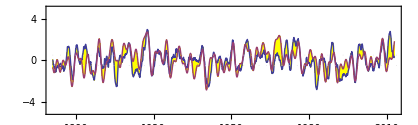

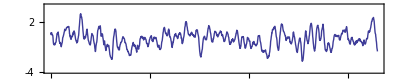

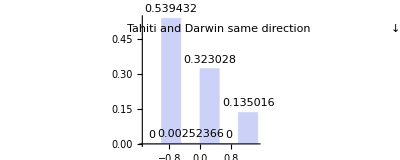

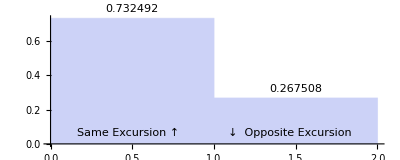

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
(* ################################### Barebones SOIM ##################################### *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 8;  WinLoFilter = 445;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLowFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLowFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 0*MeanFilter[NINO34[[All,2]],WinLowFilter]; *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* shaping functions for capturing model of TSI *)

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.97258;  MW := 0.123;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 1.05*Sin[CW*(x+0.89)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.22/MW)];    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .35*(.071*qbo[x+.54]-.019*cw[x+1.68])+.0123*mw[x];
Hill[x_] := 1.41*(-.54*cw[x+2.78]*(1+0.65*qbo[x+0.1])-.288*qbo[x+.8] -0*.013*mw[x-0.0]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0019, y[52]==.0026}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.9]; Thresh = 0.5;
SOIM = Table[{YEAR+x, First[-119.1*y[x+.7+dilate[x] -0.27*Sin[2*Pi*(x-34)/99]] /. SOLN]},{x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
  SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
  ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
 ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

{char t,4.2342,-0.366608, Years from,1881.,to,2013.,CC,59.0732,58.0515,-1.02173}

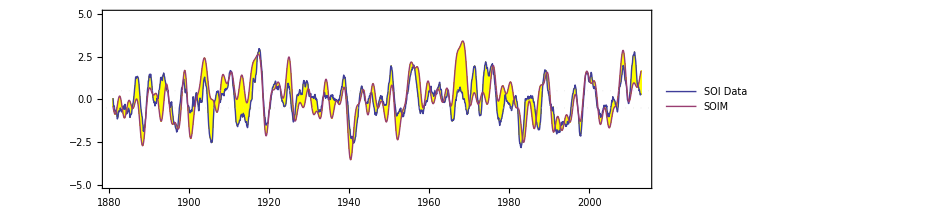

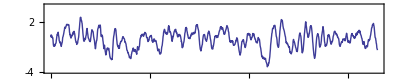

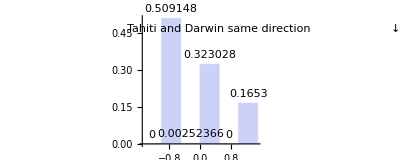

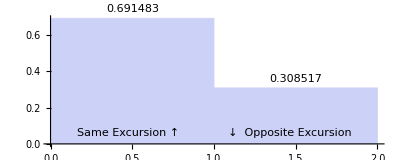

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
(* TTTTTTTTTTTT SSSSSSSSSSSSSSSSSSSSSSSSSSSSS IIIIIIIIIIIIIIIIIIIII *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 8;  WinLoFilter = 445;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLowFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLowFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 0*MeanFilter[NINO34[[All,2]],WinLowFilter]; *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
sig2[x_, W_, T1_, T2_] := -1/(1+Exp[W*(x-T1)])+1/(1+Exp[W*(x-T2)]); 
sigmoid[x_, T_] := 1/(1+Exp[2.7*(x-T)]); 

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  TS = 0.5909;  CF = 2.202;  CW = 0.97258;  MW := 0.123;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 1.05*Sin[CW*(x+0.89)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.22/MW)];    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
tsi[x_] := 1.2*((Cos[TS*x+.357]*(1+3.5*Sin[(x-35.4)/217]) +  (* TSI time series low-pass filtered *)
         .6*sig2[x,5.7,25.1,28.]+  2.5*sig2[x,1.6,87.9,89.6])*((1+.3*sigmoid[x,106.4])/1.3));
(* tsi[x_] := (tsi0[x])^2 * Sign[tsi0[x]]; *)

(* RHS[x_]:= .89*(.063*qbo[x+.5]*(1+.1*tsi[x-1.1])-.0194*cw[x+1.67]-.012*tsi[x-4.2])+.018*mw[x];
Hill[x_] := 1.32*(.37*tsi[x-1.6]-.52*cw[x+2.94]-.24*qbo[x+.6]*(1-.54*tsi[x-3.1])) ; *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .33*(.07*qbo[x+.53]*(1-0*.031*tsi[x-3.])-.019*cw[x+1.68])+.0123*mw[x] -0*.0004*tsi[x-2.92] ;
Hill[x_] := 1.4*(0*.05*tsi[x-0.56]-.59*cw[x+2.8]*(1+0.7*qbo[x+0.1])-.28*qbo[x+.8]*(1-0*.09*tsi[x-0.3])) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0014, y[52]==.0028}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.27*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.9]; Thresh = 0.5;
SOIM = Table[{YEAR+x, 2.5*0.19*tsi[x-2.9] + First[-119.1*y[x+.7+dilate[x] ] /. SOLN]},{x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
  SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
  ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

{char t,4.2342,0.0242501, Years from,1881.,to,2013.,CC,58.4168,62.4453,4.02859}

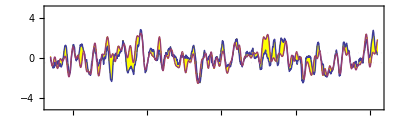

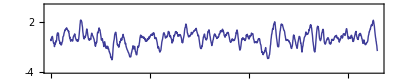

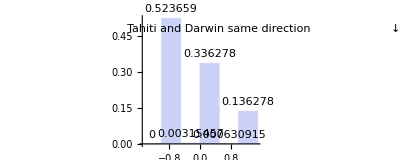

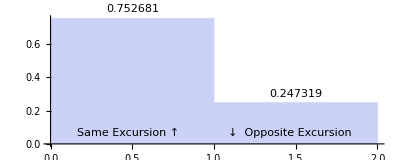

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
(* TTTTTTTTTTTT SSSSSSSSSSSSSSSSSSSSSSSSSSSSS IIIIIIIIIIIIIIIIIIIII *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 445;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLowFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLowFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 0*MeanFilter[NINO34[[All,2]],WinLowFilter]; *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*tsi0[x+0.52];

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.97258;  MW := 0.124;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 1.05*Sin[CW*(x+0.89)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.3/MW)];    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .34*(.067*qbo[x+.54]-.019*cw[x+1.59])+.013*mw[x] ;
Hill[x_] := 1.39*(-.59*cw[x+2.8]*(1+0.67*qbo[x+0.1])-.31*qbo[x+.8]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0016, y[52]==.0025}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.26*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.0]; Thresh = 0.5;
SOIM = Table[{YEAR+x, 0.39*tsi[x-3.0]*(1+0.82*qbo[x+1.15]) + First[-100.1*y[x+.71+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
  ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

{char t,4.2342,0.067233, Years from,1881.,to,2013.,CC,66.2393,66.3899,0.15066}

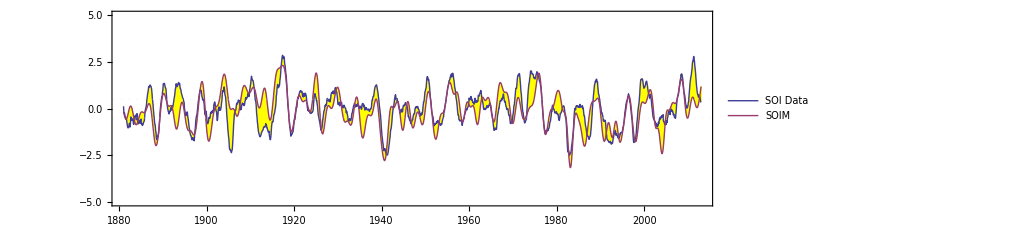

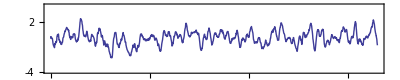

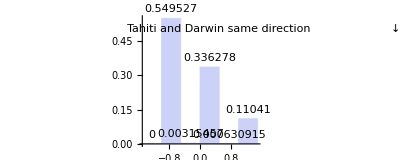

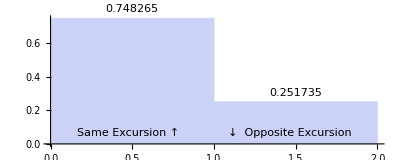

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
(* TTTTTTTTTTTT SSSSSSSSSSSSSSSSSSSSSSSSSSSSS IIIIIIIIIIIIIIIIIIIII *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52])^2 * Sign[tsi0[x+0.52]]  + 0*ga[x,89.6];

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.97257;  MW := 0.125;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 1.05*Sin[CW*(x+0.89)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.4/MW)];    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .33*(.068*qbo[x+.54]-.019*cw[x+1.61])+.0123*mw[x] + 0.014*ga[x,89.6];
Hill[x_] := 1.39*(-.56*cw[x+2.8]*(1+0.68*qbo[x+0.1])-.29*qbo[x+.8]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0007, y[52]==.0026}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.29*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.0]; Thresh = 0.5;
SOIM = Table[{YEAR+x, +0.12*qbo[x+0.48] + 4.5*0.38*tsi[x-3.0]*(1+0.82*qbo[x+1.15]) + First[-103.1*y[x+.71+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

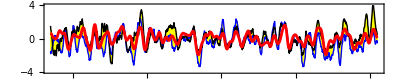

86.6959

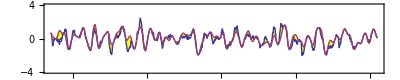

72.4139

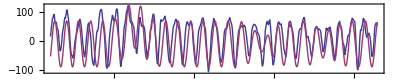

74.4284

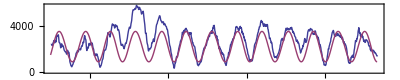

85.9157

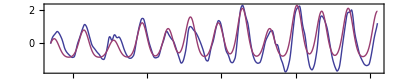

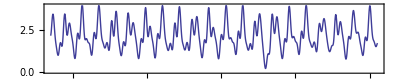

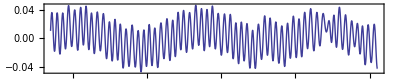

25.1107

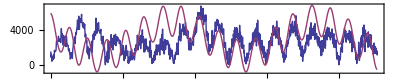

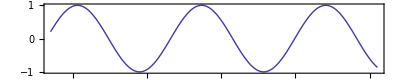

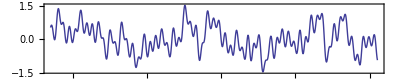

```mathematica
WinLoFilter = 445;    WinHiFilter =9;   Future=0;  Past=0; SEP=0;
R1 = -1*MeanFilter[darwin[[All,2]],WinHiFilter] + 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R2 = 1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];  
R = R1-R2;
SOIT1 = Table[{1880+i/12, 2*R1[[i]]+SEP},{i,STRT,LNGTH,1}];    
SOIT2 = Table[{1880+i/12, 2*R2[[i]]+SEP},{i,STRT,LNGTH,1}]; 
(* b > (a < c ? a : c) && b < (a > c ? a : c) *)  
InBetween[a_,b_,x_] := If[a>b, If[x<a,If[x>b,x,b],a], If[x<b,If[x>a,x,a],b]];
(* PickBest[a_,b_,m_,x_] := If[Abs[a-x]<Abs[b-x], If[Abs[a-x]<Abs[m-x], x, a], If[Abs[b-x]<Abs[m-x], x, b]] + SEP;
PickBest[a_,b_,m_,x_] :=  InBetween[a,b,x]; *)
(* PickBest[a_,b_,m_,x_] := If[Abs[a-x]<Abs[b-x], a, b] + SEP;  *)
BEST1 = Table[{1880+i, InBetween[2*R1[[i*12]], 2*R2[[i*12]],  SOIM[[i*12-STRT+1,2]] ]},{i,STRT/12,LNGTH/12,1/12}]; 
ListLinePlot[{SOIT1,SOIT2,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False,Filling->{1->{{2},Yellow}},
    PlotLegends->{"-2x Darwin","2x Tahiti","SOIM"}, PlotStyle->{Blue,Black,Directive[Red,AbsoluteThickness[2]]},AspectRatio->0.2]
BESTCC = 100*Correlation[BEST1,SOIM][[2,2]]
ListLinePlot[{BEST1,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},
    PlotLegends->{"best SOI Data","SOIM"}, AspectRatio->0.2, GridLines->{None,{{-0.25,Dotted},{0.25,Dotted}} }]
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70hPa", "Model"}]
CWM = Table[{1880+i, 1500*(cw[i]-0*mw[i])+2200},{i,50,133+2/12, 1/12}];
CWDATA = MeanFilter[CW1[[All,2]],3];
CWFiltered = Table[{1930+i/12, CWDATA[[i]]},{i,1,999,1}]; 
100*Correlation[CWFiltered,CWM][[2,2]]
ListLinePlot[{CWFiltered,CWM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 1*MeanFilter[TSID[[All,2]],215]; 
TSIT = Table[{1880+i/12, 100*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -tsi[x]},{x,STRT/12,LNGTH/12, 1/12}];
100*Correlation[TSIT,TSIM][[2,2]]
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"Mean-filtered\nTSI", "Model"}] 
hill = Table[{1880+i, CF+Hill[i]},{i,1,133+2/12, 1/12}];
ListLinePlot[hill, PlotRange->{0,4}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"CF+HillMathieu\nmodel"}] 
rhs = Table[{1880+i, RHS[i]},{i,1,133+2/12, 1/12}];
ListLinePlot[rhs, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"RHS model"}] 
CWM = Table[{1880+i, 2000*(cw[i]+mw[i])+3000},{i,20,133+2/12, 1/12}];
100*Correlation[CW0,CWM][[2,2]]
ListLinePlot[{CW0,CWM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
(* Export["fitSoimRHS.csv", rhs];  71.4381 *)
mws = Table[{1880+i, mw[i]},{i,1,133+2/12, 1/12}];
ListLinePlot[mws, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"MW model"}] 
res= Table[{1880+i, Resid[i]},{i,1,133+2/12, 1/12}];
ListLinePlot[res, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"Residual model"}]
```

```mathematica
Print[InBetween[4,1,2]]
Print[InBetween[4,1,5]]
Print[InBetween[4,1,-1]]
Print[InBetween[1,4,2]]
Print[InBetween[1,4,5]]
Print[InBetween[1,4,-1]]
```

True

False

False

True

False

False

{char t,4.2342,0.189464, Years from,1881.,to,2013.,CC,38.0922,64.2363,26.144}

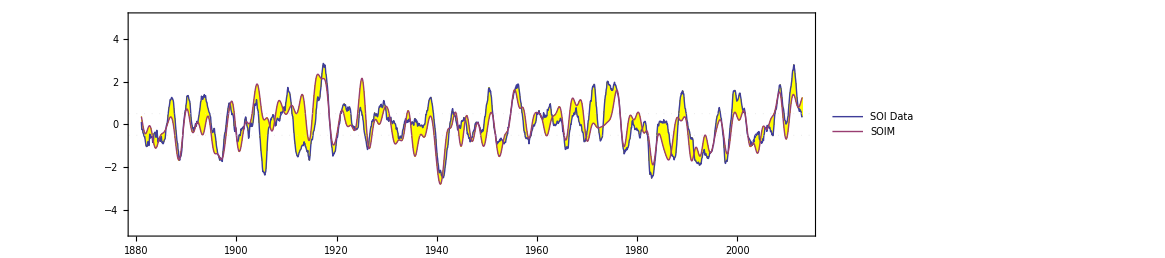

```mathematica
(* TTTTTTTTTTTT SSSSSSSSSSSSSSSSSSSSSSSSSSSSS IIIIIIIIIIIIIIIIIIIII *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*tsi0[x+0.52];

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.98; MW := 0.125;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 0.98*Sin[CW*(x+0.4)+0.12*Sin[0.361*(x+6.1)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.4/MW)];    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .3*(.066*qbo[x+.54]-.018*cw[x+1.5])+.0123*mw[x] + 0.014*ga[x,89.6];
Hill[x_] := 1.4*(-.6*cw[x+2.8]*(1+0.4*qbo[x+0.1])-.29*qbo[x+.8]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.001, y[52]==.0026}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.29*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.0]; Thresh = 0.5;
SOIM = Table[{YEAR+x, +0.12*qbo[x+0.48] + 1*0.38*tsi[x-3.0]*(1+0.82*qbo[x+1.15]) + First[-103.1*y[x+.71+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
```

{char t,4.2342,0.00491751, Years from,1881.,to,2013.,CC,61.588,61.588,-2.13163×10^-14}

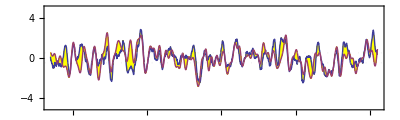

```mathematica
(* TTTTTTTTTTTT SSSSSSSSSSSSSSSSSSSSSSSSSSSSS IIIIIIIIIIIIIIIIIIIII *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*tsi0[x+0.52];

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.955; MW := 0.125;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := 1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
cw[x_] := 1.1*Sin[CW*(x+2.3)+0.2*Sin[0.361*(x+6.6)]] ;  (* Chandler wobble time series *)
mw[x_] := Cos[MW*(x-1.4/MW)] ;    (* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .31*(.068*qbo[x+.54]-.024*cw[x+1.6])+.0123*mw[x]+ 0.014*ga[x,89.6];
Hill[x_] := 1.4*(-.55*cw[x+3.0]*(1+0.4*qbo[x+0.1])-.29*qbo[x+.8]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0007, y[52]==.0026}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.29*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.0]; Thresh = 0.5;
SOIM = Table[{YEAR+x, +0.12*qbo[x+0.48] + 1*0.38*tsi[x-3.0]*(1+0.82*qbo[x+1.15]) + First[-103.1*y[x+.71+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
```

{char t,4.2342,-0.062323, Years from,1881.,to,2013.,CC,63.2139,63.1652,-0.0486967}

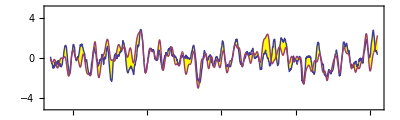

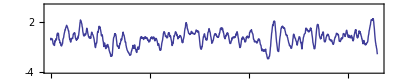

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52])^2*Sign[tsi0[x+0.52]]  + 0*ga[x,89.6];

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7002;  CF = 2.202;  CW = 0.97257;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := +1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
QBOTra = 72.7;
qbo[x_] := 1.0*((1-sigmoid[x,QBOTra])*Cos[QB*x+1.21+0.4*Sin[.515*x-2] ] +
         sigmoid[x,QBOTra]*Cos[QB*x+1.21+.4*Sin[.515*x-2]+0*0.17*Sin[0.117*x+0.2] ]);     (* QBO time series *)
cw[x_] := +1.05*Sin[CW*(x+0.89)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)

GWI = 6.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
mw[x_] := .013*Cos[MW*(x-1.5/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)

(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .33*(.065*qbo[x+.53]-.018*cw[x+1.63])+ mw[x]+ 0*ga2[x,89.6] ; (*  *)
Hill[x_] := 1.4*(-.67*cw[x+2.8]*(1+0.6*qbo[x+0.1])-.3*qbo[x+.85]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0007, y[52]==.0026}, y, {x, -20, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.29*Sin[2*Pi*(x-34)/99] -0.0*Sin[0.07*x+5.] - 0*0.04*Cos[2*Pi*x-0.0]; Thresh = 0.5;
SOIM = Table[{YEAR+x, +0.12*qbo[x+0.48] + 4.4*0.38*tsi[x-2.9]*(1+0.61*qbo[x+1.2]) + First[-103.1*y[x+.73+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-Thresh,Dotted},{Thresh,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
(*ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
*)
```

{char t,4.2342,-0.0873532, Years from,1881.,to,2013.,CC,25.874,66.3697,40.4957}

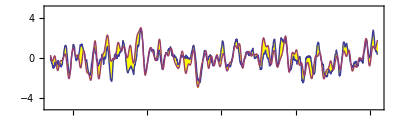

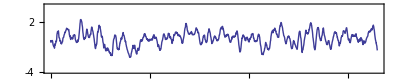

71.4758

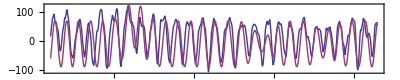

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52])^2*Sign[tsi0[x+0.52]]  + 0*ga[x,89.6];
tsi[x_] := 5.93*(tsi0[x+0.52]);

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6989;  CF = 2.202;  CW = 0.9726;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := +1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
QBOTra = 74;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.1+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := .0131*Cos[MW*(x-1.48/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
(* 0*.0021*Sin[2*Pi/9.06*(x+4.8)] 0*.1*Cos[2*Pi/9.06*(x+1.8)]*(1+1.0*qbo[x+0.0]) *)
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .34*(.066*qbo[x+.52]-.018*cw[x+1.6])+ mw[x] + + 0.0*ga2[x,89.6]; (*  *)
Hill[x_] := 1.49*(-.68*cw[x+2.8]*(1+0.53*qbo[x+0.1])-.28*qbo[x+0.85] - 1*mw[x+12]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0007, y[52]==.0027}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.26*Sin[2*Pi*(x-37)/110] -0.0*Sin[0.07*x+5.] - 0*0.05*Cos[2*Pi*x+0.2]; 
SOIM = Table[{YEAR+x, 0.39*tsi[x-3.1]*(1+0.6*qbo[x+1.1]) + First[-100*y[1.0005*x+.75+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
(* ST = -Table[{YEAR+i/12, RT[[i]]},{i,STRT,LNGTH,1}];   
SD = Table[{YEAR+i/12, RD[[i]]},{i,STRT,LNGTH,1}];   
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
*)
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
```

{0.00860393,Years from,1651.,to,1976.,CC,66.3316,33.6144,-32.7172}

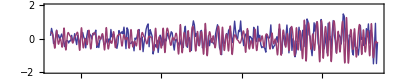

```mathematica
SEP = 0;  (* ###################################################################### *)
STRT=1;   STRTY=1650+STRT; (* This is just two components *)
LNGTH=326; ENDY=1650+LNGTH;
SOIT = Table[{UEP[[i,1]], SEP+UEP[[i,2]]},{i,STRT,LNGTH,1}];  
SHFT=1.7;
NDSolve[{y''[x]- 0.011*y'[x]+(2.318 +1.48*Sin[0.763*(x+2.42+SHFT)])*y[x]  
         == -0.018*Cos[1.026*(x-2.03+SHFT)] 
         - 0.0127 - 0.000043*x ,
         y'[52.0]==-0.0078, y[52.00]==+0.042}, y, {x, -230, 100}, MaxSteps->100000];   
SSX = %;
SOIM = Table[{1880.0+x, First[25*y[x] /. SSX]},{x,-231+STRT,-231+LNGTH, 1}];     
SOIG = Table[{1880.0+x, First[25*y[x] /. SSX]},{x,-231+STRT,-231+LNGTH, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]]; 
Var = Variance[SOIT]-Variance[SOIM];
Print[{Var[[2]], "Years from", N[STRTY], "to", N[ENDY], "CC", OldCC,  NewCC, NewCC - OldCC }]
ListLinePlot[{SOIT, SOIG}, PlotRange->{-2.0,SEP+2.0}, Frame->True, Axes->False, 
              PlotLegends->{"EOP", "SOIM"}, AspectRatio -> 0.2]
```

{0.0698671,Years from,1651.,to,1976.,CC,24.0455,24.3419,0.2964}

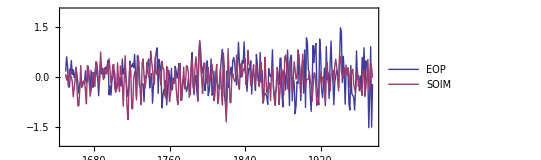

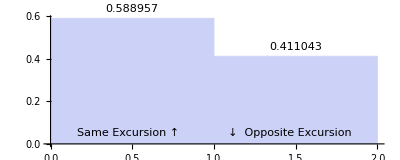

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.717;  CF = 2.196;  CW = 0.9732;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := +1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
QBOTra = 74;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+0.99+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := .0131*Cos[MW*(x-1.48/MW)] ;    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
(* 0*.0021*Sin[2*Pi/9.06*(x+4.8)] 0*.1*Cos[2*Pi/9.06*(x+1.8)]*(1+1.0*qbo[x+0.0]) *)
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .34*(.066*qbo[x+.57]-.018*cw[x+1.6])+ mw[x] ; (*  *)
Hill[x_] := 1.49*(-.68*cw[x+2.8]*(1+0.53*qbo[x+0.24])-.28*qbo[x+0.92] - 1*mw[x+12]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0007, y[52]==.0027}, y, {x, -250, 160}];  
SEP = 0;  (* ###################################################################### *)
dilate[x_] := -0.1*Sin[2*Pi*(x-37)/110] -0.0*Sin[0.07*x+5.] - 0.05*Cos[2*Pi*x+0.2]; 
STRT=1;   STRTY=1650+STRT; (* 230 =1880  326  0.78 *)
LNGTH=326; ENDY=1650+LNGTH;
SOIT = Table[{UEP[[i,1]], SEP+UEP[[i,2]]},{i,STRT,LNGTH,1}];  
SHFT=1.7;                         (* 0.35  *)
(* SOIM = Table[{1880.0+x, 35*First[y[x+If[x<0,1.22,0.18]+dilate[x-39.5]] /. SOLN]},{x,-231+STRT,-231+LNGTH, 1}];  *)   
SOIM = Table[{1880.0+x, 35*First[y[0.995*x+0.45+0*dilate[x-39.5]] /. SOLN]},{x,-231+STRT,-231+LNGTH, 1}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]]; 
Var = Variance[SOIT]-Variance[SOIM];
Print[{Var[[2]], "Years from", N[STRTY], "to", N[ENDY], "CC", OldCC,  NewCC, NewCC - OldCC }]
ListLinePlot[{SOIT, SOIM}, PlotRange->{-2.0,SEP+2.0}, Frame->True, Axes->False, 
              PlotLegends->{"EOP", "SOIM"}, AspectRatio -> 0.4]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

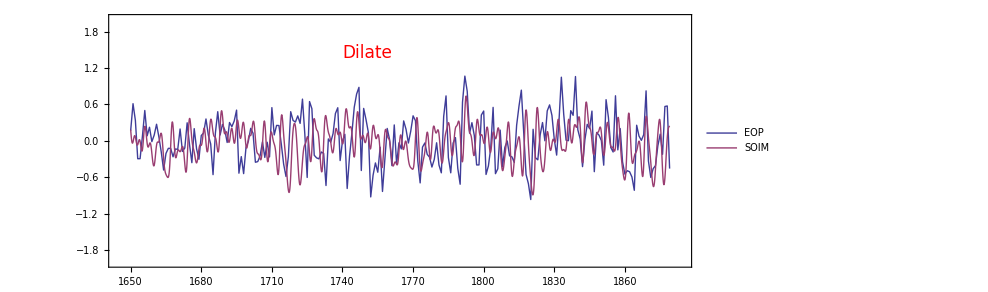

{char t,4.23998,0.00623805, Years from,1881.,to,2013.,CC,66.8283,66.6567,-0.171593}

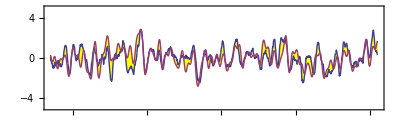

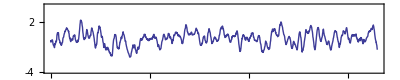

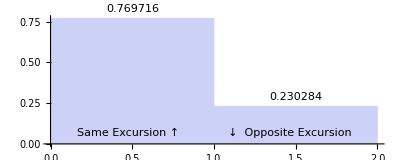

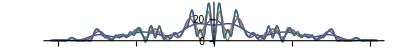

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
(* QB=2.6989;  CF = 2.202;  CW = 0.9726;  MW := 0.126; *)
QB=2.6989;  CF = 2.196;  CW = 0.9732;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 75;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.17+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] + 0*0.04*Sin[CW/2*(x+5.5)] ;  (* Chandler wobble time series *)
mw[x_] := .012*Cos[MW*(x-1.5/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
modtsi[x_] := tsi[x-3.1]*(1+0.6*qbo[x+1.1]);
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .34*(.066*qbo[x+.52]-.018*cw[x+1.6])+ mw[x] + 0*0.0009*modtsi[x-3.2] + 0.0*ga2[x,89.6]; (*  *)
Hill[x_] := 1.49*(-.68*cw[x+2.8]*(1+0.53*qbo[x+0.1])-.28*qbo[x+0.85] - 1*mw[x+12]) - 0*0.04*modtsi[x-3.6];
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0005, y[52]==.0025}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.25*Sin[2*Pi*(x-36)/120] -0.0*Sin[0.07*x+5.] - 0*0.05*Cos[2*Pi*x+0.2]; 
SOIM = Table[{YEAR+x, 0*17*mw[x]+0*0.15*cw[x+0.95] -0*0.4*Sin[CW/2*(x+6.4)] + 0.39*modtsi[x] + First[-98*y[1*x+.75+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
(*
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]*)
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
(*
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
*)
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,100,500,100}],{ω,-π/10,π/10},PlotRange->All,AspectRatio->0.1]
```

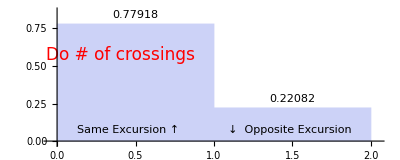

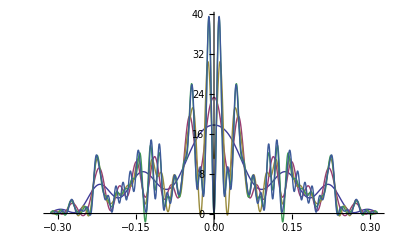

{char t,4.23901,0.015034, Years from,1881.,to,2013.,CC,47.1113,47.1226,0.0113326}

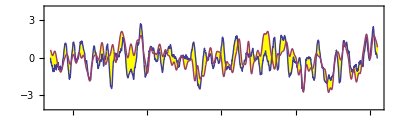

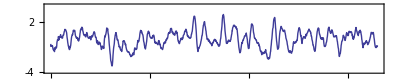

71.5509

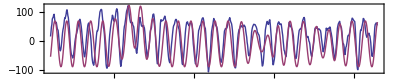

```mathematica
(* THIS is USING chain-rule expansion of wave equation *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   0*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
(* QB=2.6989;  CF = 2.202;  CW = 0.9726;  MW := 0.126; *)
QB=2.6989;  CF = 2.197;  CW = 0.9735;  MW := 0.125;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := +1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
QBOTra = 74;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.2+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := .012*Cos[MW*(x-1.49/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
(* 0*.0021*Sin[2*Pi/9.06*(x+4.8)] 0*.1*Cos[2*Pi/9.06*(x+1.8)]*(1+1.0*qbo[x+0.0]) *)
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .041*(.05*qbo[x+0.4]-.08*cw[x+1.6]) +0.002*Sin[CW/2*(x-7.1)] + mw[x] + 0.0*ga2[x,89.6]-0*0.1*Cos[2*Pi*x+0.4]+0*0.06*Cos[4*Pi*x+0.5]; (*  *)

Hill[x_] := 1.0*(1+0.7*Sin[CW*x-3.4] -0*0.11*Sin[2*Pi/9.17*x +0.21]); 
(* Hill[x_] := 1-18*RHS[x+0.9]; *)
SOLN = NDSolve[{y''[x]- Hill'[x]/Hill[x]*y'[x]+2.199/Hill[x]*y[x] == RHS[x], 
y'[52]==+.001, y[52]==.0013}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := 0*0.26*Sin[2*Pi*(x-37)/110] -0.0*Sin[0.07*x+5.] - 0*0.05*Cos[2*Pi*x+0.2]; 
SOIM = Table[{YEAR+x, 0.7*tsi[x-2.6]*(1+0.6*qbo[x+1.1]) + First[-80*y[1.001*x+0.9+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  

QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
```

{char t,4.23998,-0.0499205, Years from,1881.,to,2013.,CC,43.4063,60.3672,16.9609}

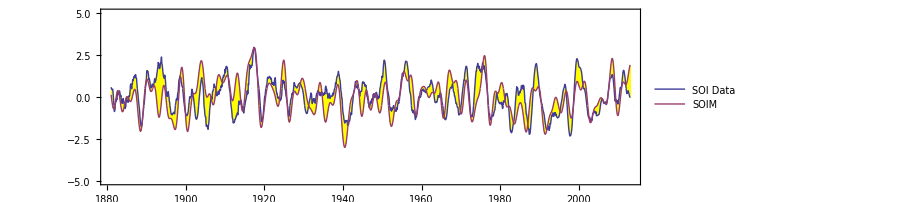

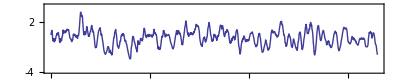

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
(* RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter]; *)
TF = MeanFilter[tahiti[[All,2]],WinHiFilter]*2 - 0*MeanFilter[tahiti[[All,2]],WinLowFilter]*2;
DF = -MeanFilter[darwin[[All,2]],WinHiFilter]*2 + 0*MeanFilter[darwin[[All,2]],WinLowFilter]*2; 
R = -2*MeanFilter[NINO34[[All,2]],WinHiFilter] + 0*MeanFilter[NINO34[[All,2]],WinLoFilter]; 
(* R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); *)
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
InBetween[a_,b_,x_] := Median[{a,b,x}];
SOIT = Table[{YEAR+i/12, InBetween[TF[[i]], DF[[i]], R[[i]] ]},{i,STRT,LNGTH,1}]; 
(* SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];  *) 

(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52])^2*Sign[tsi0[x+0.52]]  + 0*ga[x,89.6];
tsi[x_] := 5.93*(tsi0[x+0.52]);

(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
(* QB=2.6989;  CF = 2.202;  CW = 0.9726;  MW := 0.126; *)
QB=2.6989;  CF = 2.196;  CW = 0.9732;  MW := 0.127;
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] := +1.0*Cos[QB*x+1.21+.4*Sin[.515*x-2.] ];     (* QBO time series *)
QBOTra = 75;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.2+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := .012*Cos[MW*(x-1.5/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
(* 0*.0021*Sin[2*Pi/9.06*(x+4.8)] 0*.1*Cos[2*Pi/9.06*(x+1.8)]*(1+1.0*qbo[x+0.0]) *)
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .42*(.067*qbo[x+.53]-.018*cw[x+1.5])+ mw[x] + 0.0*ga2[x,89.6]; (*  *)
Hill[x_] := 1.48*(-.69*cw[x+2.85]*(1+0.66*qbo[x+0.19])-.29*qbo[x+0.8] - 1*mw[x+13]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.001, y[52]==.0023}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.23*Sin[2*Pi*(x-40)/110] -0.0*Sin[0.07*x+5.] - 0*0.05*Cos[2*Pi*x+0.2]; 
SOIM = Table[{YEAR+x, 0.37*tsi[x-2.9]*(1+0.6*qbo[x+1.2]) + First[-92*y[1.0005*x+.7+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
(*
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
*)
```

{char t,4.23998,0.0410113, Years from,1881.,to,2013.,CC,-44.7874,70.5563,115.344}

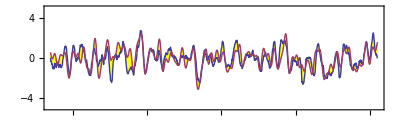

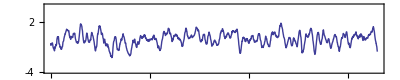

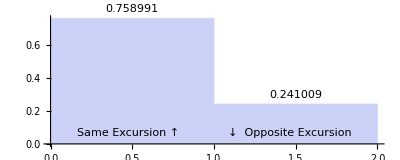

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
RT = MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];
RD = MeanFilter[darwin[[All,2]],WinHiFilter] - 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   0*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* shaping functions for capturing model of TSI *)
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6989;  CF = 2.196;  CW = 0.9732;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 75;
GWI = 5.9; ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
 qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.17+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] + 0*0.03*Sin[CW/2*(x+5.5)] ;  (* Chandler wobble time series *)
mw[x_] := .012*Cos[MW*(x-1.5/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
modtsi[x_] := tsi[x-3.1]*(1+0.6*qbo[x+1.1]);
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .33*(.066*qbo[x+.52]-.018*cw[x+1.6])+ mw[x] +0.000013*x; (* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.5*(-.68*cw[x+2.8]*(1+0.53*qbo[x+0.1])-.28*qbo[x+0.85] - 1*mw[x+12]) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0005, y[52]==.0025}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.25*Sin[2*Pi*(x-36)/120] ; 
SOIM = Table[{YEAR+x, 17*mw[x]+0.15*cw[x+0.95] -0.4*Sin[CW/2*(x+6.4)] + 0.39*modtsi[x] + First[-98*y[1*x+.75+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
(*
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.32]-10},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]*)
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
(*
SBIN = (Sign[ST[[All,2]]]+Sign[SD[[All,2]]])*Sign[SOIM[[All,2]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑                                        Tahiti and Darwin same direction                       ↓  Opposite Excursion"},Top]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,100,500,100}],{ω,-π/10,π/10},PlotRange->All,AspectRatio->0.1]
*)
```

{-4.13212,CC,69.7686,-44.7874,-114.556}

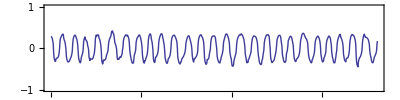

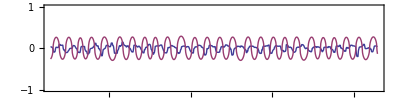

7.88115

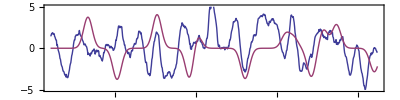

6.44379

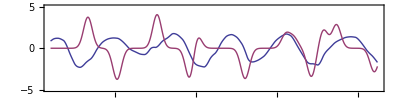

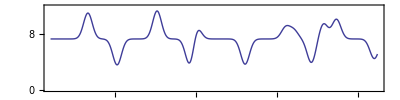

```mathematica
(* This is for exporting files *)
Q = MedianFilter[QBO[[All,2]],2] - 1*MeanFilter[QBO[[All,2]],160];  (* QBO data 20 hPa *)
TF = -MeanFilter[tahiti[[All,2]],9]*2 ;
DF = MeanFilter[darwin[[All,2]],9]*2; 
SEP=0.0;  
QBOT = Table[{QBO[[i,1]], SEP+0.0011*Q[[i]]},{i,15,736,1}];   
ga[x_,T_] := Exp[-(x-T)^2/7.6];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(0*1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_,SHFT_] := 1.8*(tsi0[x+2.3+SHFT])+0.32;
ga[x_,T_] := 1.01*Exp[-(x-T)^2/1.3];
velocity[x_, Ph_] := Sign[y[x+Ph]]*Sqrt[Abs[y[x+Ph]]]; (* square root of energy *)
CF = 7.341;
Hill[x_] := CF + 1.0*(3.7*(ga[x,7.0]-ga[x,12.4])+4*(ga[x,19.8]-ga[x,25.9])+
               2*(ga[x,27.1]-ga[x,36.0]) - 1.63*(ga[x,36.2]-ga[x,43.6]) + 1.2*(ga[x,45.1]-ga[x,48.3]) -
               2.2*(ga[x,48.4]-ga[x,50.6]) + 2.8*(ga[x,53]-ga[x,60.0]));
NDSolve[{y''[x]+0*y'[x]+1.0*(Hill[x])*y[x] ==  0.0*Cos[4*Pi*x-0.1],
         y'[0.0]==0.27, y[0.0]==0.3}, y, {x, -2.0, 102.0}, MaxSteps->100000]; 
(* ------------------------------------------------------------------ *)
QBOM = Table[{1953.0+x, 0.47*First[ velocity[x,0.14] /. %] }, {x,15/12,736/12,1/12}];
SOIT = Table[{1880+i/12, 1*(TF[[i]]+DF[[i]])},{i,877,1603,1}]; 
EV = Table[{1953.0+x, Hill[x]-CF }, {x,1/12,727/12,1/12}];
HILL = Table[{1953.0+x, Hill[x] }, {x,1/12,727/12,1/12}];
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]];
Var = Variance[QBOT]-Variance[QBOM];
Print[{ 100*Var[[2]], "CC", OldCC,  NewCC, NewCC - OldCC}]
SDIFF = QBOT[[All,2]]-QBOM[[All,2]];  
ListLinePlot[{SDIFF}, PlotRange->{-1,1}, Frame->True, Axes->True,  
              PlotLegends->{"QBO-Model"}, AspectRatio -> 0.25]
(* Export["qbo_0.2a_contour.txt", QBOM]; *)
ListLinePlot[{QBOT, QBOM}, PlotRange->{-1,1+SEP}, Frame->True, Axes->False, 
              PlotLegends->{"QBO 20hPa", "Model"}, AspectRatio -> 0.25]
100*Correlation[SOIT,EV][[2,2]]
ListLinePlot[{SOIT,EV}, PlotRange->{-5,5}, Frame->True, Axes->False, 
              PlotLegends->{"SOI", "Hill"}, AspectRatio -> 0.25]
TSDATA= -1*MeanFilter[TSID[[All,2]],0] + 1*MeanFilter[TSID[[All,2]],215]; 
TSIT = Table[{1880+i/12, 100*TSDATA[[i]]},{i,877,1603,1}]; 
100*Correlation[TSIT,EV][[2,2]]
ListLinePlot[{TSIT,EV}, PlotRange->{-5,5}, AspectRatio->0.25, Frame->True, Axes->False, PlotLegends->{"TSI","Hill"}] 
ListLinePlot[{HILL}, PlotRange->{0,12}, Frame->True, Axes->False, 
              PlotLegends->{"Hill"}, AspectRatio -> 0.25]
```

{char t,4.23998,0.00433689, Years from,1881.,to,2013.,CC,70.4237,70.4237,4.26326×10^-14}

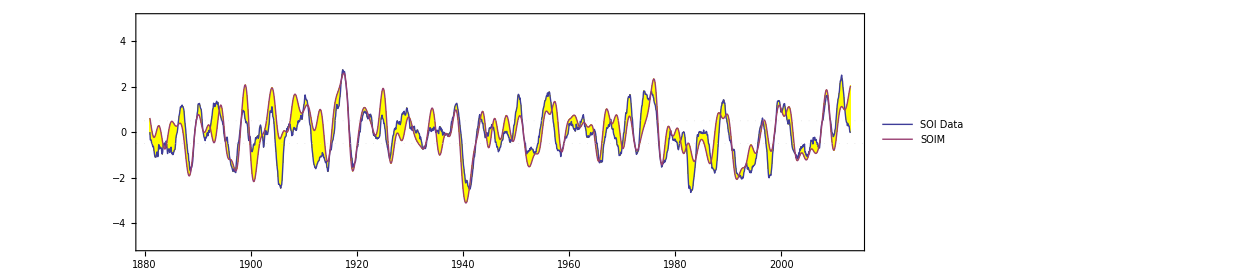

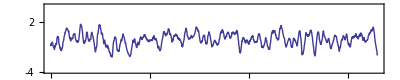

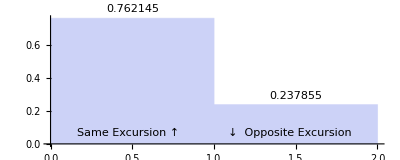

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 440;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   0*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(+0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6989;  CF = 2.196;  CW = 0.9732;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 75;
qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.17+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
cw[x_] := +1.06*Sin[CW*(x+0.9)+0.189*Sin[0.361*(x+5.3)]] ;  (* Chandler wobble time series *)
mw[x_] := .012*Cos[MW*(x-1.5/MW)];    (* 2.1*(x)/140* inferred multi-decadal forcing,  LOD ? Markowitz wobble ? *)
modtsi[x_] := tsi[x-3.1]*(1+0.6*qbo[x+1.1]);
(* The SOIM differential equation solved with the Mathematica NDSolve function +0.0*Cos[2*Pi/1.186*x-2.2] *)
RHS[x_]:= .33*(.066*qbo[x+.52]-.018*cw[x+1.6])+ mw[x] ; (* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.5*(-.68*cw[x+2.8]*(1+0.53*qbo[x+0.1])-.28*qbo[x+0.85] ) ;
SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0005, y[52]==.0025}, y, {x, -250, 160}];  
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.25*Sin[2*Pi*(x-36)/120] ; 
SOIM = Table[{YEAR+x, 17*mw[x]+0.15*cw[x+0.95] -0.4*Sin[CW/2*(x+6.4)] + 0.39*modtsi[x] + First[-100*y[1*x+.75+dilate[x] ] /. SOLN]},
             {x,STRT/12-Past,LNGTH/12+Future, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

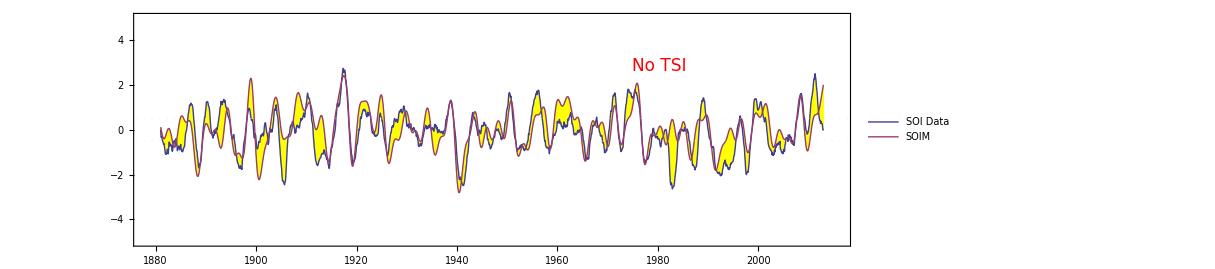

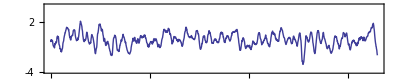

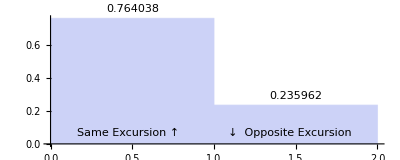

{char t,4.24578,0.0260479, Years from,1881.,to,2013.,CC,49.5259,72.4812,22.9554}

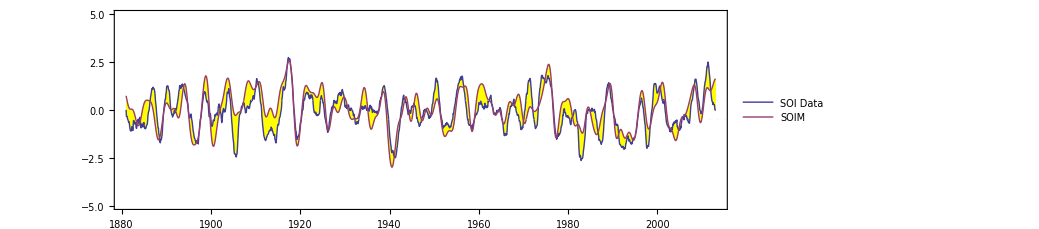

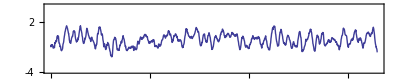

59.0385

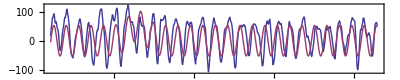

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 450;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   0*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.701; CW = 0.9731; MW := 0.125; CF = 2.19;  
mw[x_] := Cos[MW*(x-1.5/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] :=  0.66*( Cos[QB*x+1.45+0*.4*Sin[.519*x-2.1]]  +0.99*Exp[-(x-89.6)^2/5.6] );
CWT = 26;
cw[x_] := +1.12*( (1-sigmoid[x,CWT])*Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] 
                    +sigmoid[x,CWT]*Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-3.0]*(1+0.8*qbo[x+1.07]);
RHS[x_]:= .28*(0.085*qbo[x+.46]-.0145*cw[x+2.1]*(1+0.0*qbo[x+0.4]))+ 0.0115*mw[x]; 
(* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.44*(-.69*cw[x+2.71]*(1+0.77*qbo[x-0.11])-0.28*qbo[x+0.9]+ 0.0*mw[x-8] ) ;
(*SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0008, y[52]==.0023}, y, {x, -250, 160}];  *)
(* SOLN = NDSolve[{y''[x]+0.1*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[25]==.04, y[25]==.002}, y, {x, -250, 160}];  *)
SOLN = NDSolve[{y''[x]+0.001*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[2]==.009, y[2]==.0004}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.24*Sin[2*Pi*(x-33)/110] ; 
SOIM = Table[{YEAR+x, 1*(0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21]) +
             (1+0.0*tsi[x-3.1])*First[-144*y[1*x+.76+dilate[x] ] /. SOLN]        }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
SOIM2 = Table[{YEAR+x, 0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21] +
            0       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.2]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
```

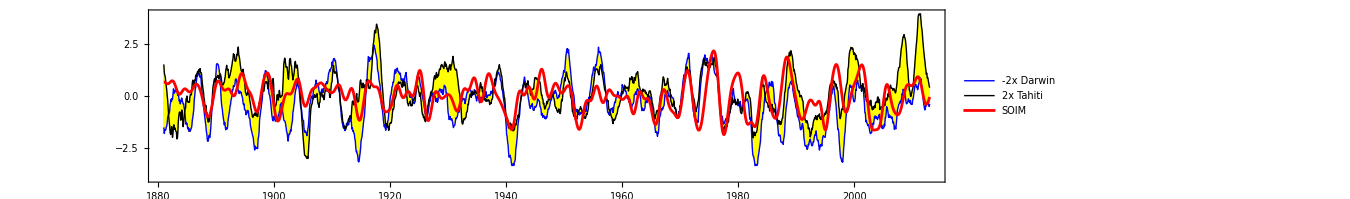

72.0375

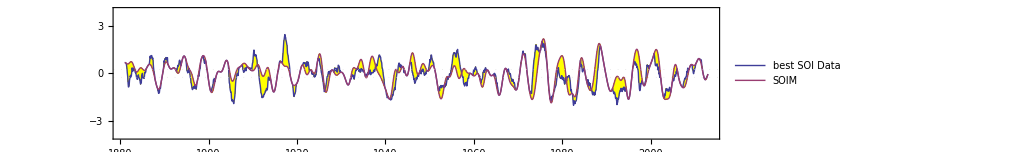

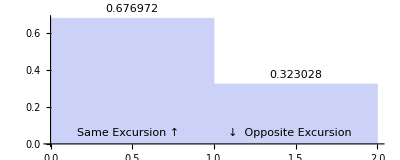

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
WinLoFilter = 445;    WinHiFilter =9;   Future=0;  Past=0; SEP=0;
R1 = -1*MeanFilter[darwin[[All,2]],WinHiFilter] + 0*MeanFilter[darwin[[All,2]],WinLoFilter];
R2 = 1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 0*MeanFilter[tahiti[[All,2]],WinLoFilter];  
R = R1-R2;
SOIT1 = Table[{1880+i/12, 2*R1[[i]]+SEP},{i,STRT,LNGTH,1}];    
SOIT2 = Table[{1880+i/12, 2*R2[[i]]+SEP},{i,STRT,LNGTH,1}]; 
(* b > (a < c ? a : c) && b < (a > c ? a : c) *)  
InBetween[a_,b_,x_] := If[a>b, If[x<a,If[x>b,x,b],a], If[x<b,If[x>a,x,a],b]];
(* PickBest[a_,b_,m_,x_] := If[Abs[a-x]<Abs[b-x], If[Abs[a-x]<Abs[m-x], x, a], If[Abs[b-x]<Abs[m-x], x, b]] + SEP;
PickBest[a_,b_,m_,x_] :=  InBetween[a,b,x]; *)
(* PickBest[a_,b_,m_,x_] := If[Abs[a-x]<Abs[b-x], a, b] + SEP;  *)
BEST1 = Table[{1880+i, InBetween[2*R1[[i*12]], 2*R2[[i*12]],  SOIM[[i*12-STRT+1,2]] ]},{i,STRT/12,LNGTH/12,1/12}]; 
ListLinePlot[{SOIT1,SOIT2,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False,Filling->{1->{{2},Yellow}},
    PlotLegends->{"-2x Darwin","2x Tahiti","SOIM"}, PlotStyle->{Blue,Black,Directive[Red,AbsoluteThickness[2]]},AspectRatio->0.2]
BESTCC = 100*Correlation[BEST1,SOIM][[2,2]]
ListLinePlot[{BEST1,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},
    PlotLegends->{"best SOI Data","SOIM"}, AspectRatio->0.2, GridLines->{None,{{-0.25,Dotted},{0.25,Dotted}} }]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

{char t,4.24288,-0.108184, Years from,1881.,to,2013.,CC,58.9983,58.9983,-2.13163×10^-14}

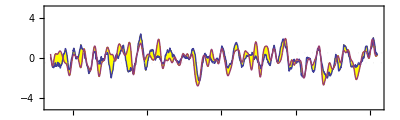

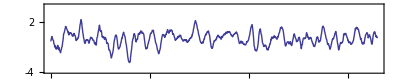

58.9791

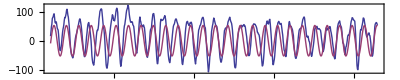

```mathematica
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 12;  WinLoFilter = 450;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   0*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];   *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.7; CW = 0.9731; MW := 0.127; CF = 2.193;  
mw[x_] := Cos[MW*(x-1.53/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] :=  0.66*( Cos[QB*x+1.45+0*.4*Sin[.519*x-2.1]]  +0.*Exp[-(x-89.6)^2/5.6] );
CWT = 26;
cw[x_] := +1.12*( Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-3.0]*(1+0.8*qbo[x+1.07]);
(* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.53*(-.46*cw[x+2.9]*(1+1.8*qbo[x+0.67])-0.33*qbo[x+0.5]) -0.093*mw[x-0.1] ;
RHS[x_]:= -0.0065*Hill[x+1.63]; 
(*SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0008, y[52]==.0023}, y, {x, -250, 160}];  *)
(* SOLN = NDSolve[{y''[x]+0.1*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[25]==.04, y[25]==.002}, y, {x, -250, 160}];  *)
SOLN = NDSolve[{y''[x]+0.0001*y'[x]+(CF+0.78*Hill[x-0.13])*y[x] == RHS[x], y'[2]==.009, y[2]==.0007}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.24*Sin[2*Pi*(x-33)/110] ; 
SOIM = Table[{YEAR+x,-0.4*mw[x]+0.09*cw[x+0.95] -0.5*Sin[CW/2*(x+6.5)]+0.42*modtsi[x]-0.3*qbo[x+0.21] +
             (1+0.0*tsi[x-3.1])*First[-123*y[1*x+0.93+dilate[x] ] /. SOLN]        }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.2]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
```

{char t,4.24578,-0.236815, Years from,1881.,to,2013.,CC,38.8761,49.5259,10.6498}

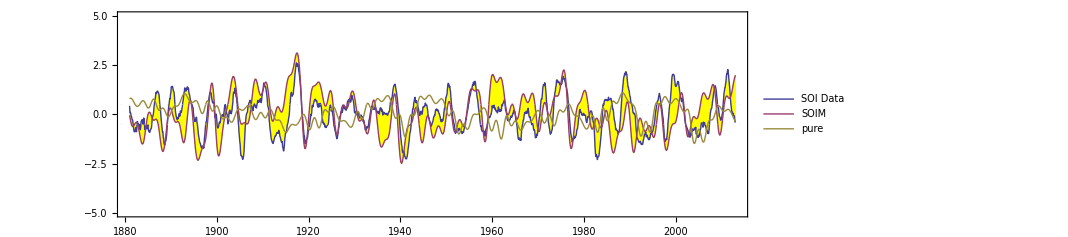

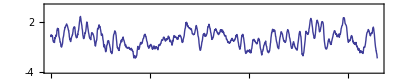

59.0385

-Graphics-

```mathematica
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 99;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.701; CW = 0.9731; MW := 0.125; CF = 2.19;  
mw[x_] := Cos[MW*(x-1.5/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
qbo[x_] :=  0.66*( Cos[QB*x+1.45+0*.4*Sin[.519*x-2.1]]  +0.99*Exp[-(x-89.6)^2/5.6] );
CWT = 26;
cw[x_] := +1.12*( (1-sigmoid[x,CWT])*Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] 
                    +sigmoid[x,CWT]*Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-3.0]*(1+0.8*qbo[x+1.07]);
RHS[x_]:= .28*(0.085*qbo[x+.46]-.0145*cw[x+2.1]*(1+0.0*qbo[x+0.4]))+ 0.0115*mw[x]; 
(* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.44*(-.69*cw[x+2.71]*(1+0.77*qbo[x-0.11])-0.28*qbo[x+0.9]+ 0.0*mw[x-8] ) ;
(*SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0008, y[52]==.0023}, y, {x, -250, 160}];  *)
(* SOLN = NDSolve[{y''[x]+0.1*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[25]==.04, y[25]==.002}, y, {x, -250, 160}];  *)
SOLN = NDSolve[{y''[x]+0.001*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[2]==.009, y[2]==.0004}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.24*Sin[2*Pi*(x-33)/110] ; 
SOIM = Table[{YEAR+x, 0*(0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21]) +
             (1+0.0*tsi[x-3.1])*First[-144*y[1*x+.76+dilate[x] ] /. SOLN]        }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
SOIM2 = Table[{YEAR+x, 0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21] +
            0       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM,SOIM2},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.2]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
```

{char t,4.24578,0.308407, Years from,1881.,to,2013.,CC,62.5049,63.2852,0.780317}

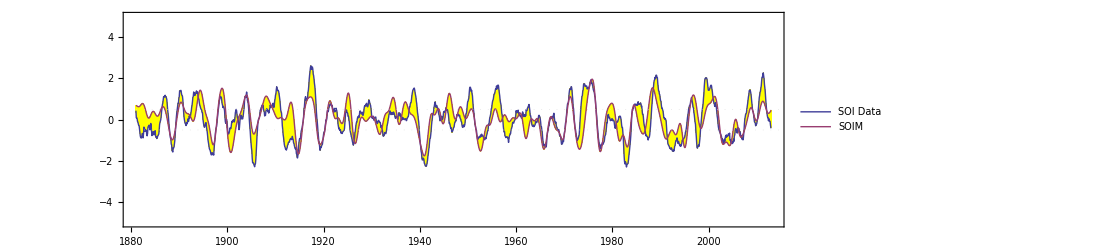

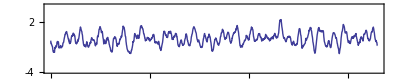

58.2313

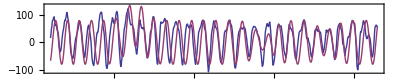

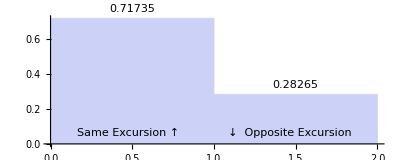

```mathematica
(* USING SQUARED TSI *)
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 9;  WinLoFilter = 99;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 

ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6989;  CF = 2.196;  CW = 0.9732;  MW := 0.126;
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 75;
qbo[x_] := + 1.0*( (sigmoid[x,QBOTra])*Cos[QB*x+1.17+.4*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)

(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.698; CW = 0.9731; MW := 0.125; CF = 2.19;  
mw[x_] := Cos[MW*(x-1.5/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
(* qbo[x_] :=  1.6*0.66*( Cos[QB*x+1.7+.4*Sin[.519*x-2.1]]  -0*0.99*Exp[-(x-89.6)^2/5.6] ); *)
CWT = 26;
cw[x_] := +0.5*1.4*( Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-3.0]*(1+0.8*qbo[x+1.07]);
RHS[x_]:= .39*(0.085*qbo[x+.5]-.0145*cw[x+2.1])+ 0.0115*mw[x]; 
(* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.8*(-.6*cw[x+2.9]*(1+0.8*qbo[x+0.0])-0.28*qbo[x+0.8]+ 0.0*mw[x-8] ) ;
(*SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0008, y[52]==.0023}, y, {x, -250, 160}];  *)
(* SOLN = NDSolve[{y''[x]+0.1*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[25]==.04, y[25]==.002}, y, {x, -250, 160}];  *)
SOLN = NDSolve[{y''[x]+0.001*y'[x]+(CF+Hill[x+0.12])*y[x] == RHS[x+0.04], y'[2]==.009, y[2]==.0004}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.24*Sin[2*Pi*(x-33)/110] ; 
SOIM = Table[{YEAR+x, 1*(0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21]) +
             (1+0.0*tsi[x-3.1])*First[-65*y[1*x+.73+dilate[x] ] /. SOLN]        }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
SOIM2 = Table[{YEAR+x, 0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21] +
            0       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.2]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.24772,0.0148833, Years from,1881.,to,2013.,CC,50.1722,70.6887,20.5165}

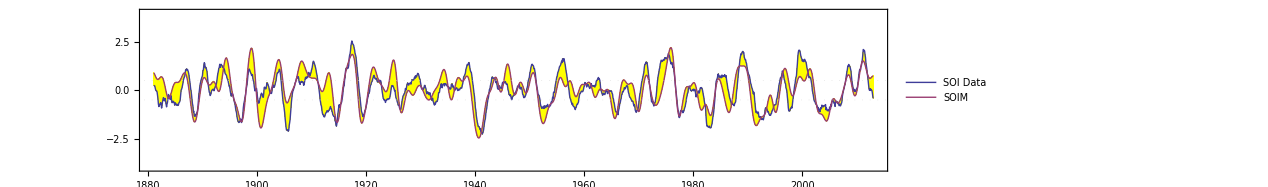

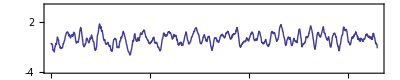

74.0695

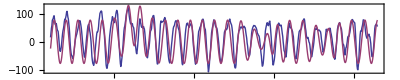

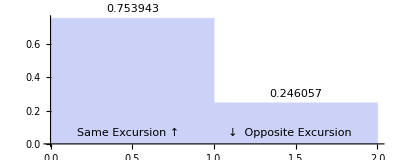

```mathematica
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 10;  WinLoFilter = 97;  Future=0;  Past=0;
R = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
(* R = -1.75*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter];  *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6989; 
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 76;
qbo[x_] := + 0.97*( (sigmoid[x,QBOTra])*Cos[QB*x+1.2+.38*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
(* closed form representations of the QBO, TSI, CW, MW data  *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
CW = 0.9731; MW := 0.1252; CF = 2.188;  
mw[x_] := Cos[MW*(x-1.5/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
(* qbo[x_] :=  1.6*0.66*( Cos[QB*x+1.7+.4*Sin[.519*x-2.1]]  -0*0.99*Exp[-(x-89.6)^2/5.6] ); *)
CWT = 26;
cw[x_] := +0.63*1.4*( Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-2.9]*(1+0.6*qbo[x+1.1]);
RHS[x_]:= .33*(0.085*qbo[x+.5]-.015*cw[x+2.0])+ 0.016*mw[x]; 
(* + 0*0.0009*modtsi[x-3.2] - 0.00*Cos[2*Pi*365/431*x-0.7] - 0.000*Sin[CW/2*(x+6.0)] + 0.0*ga2[x,89.6] *)
Hill[x_] := 1.72*(-.6*cw[x+2.9]*(1+0.58*qbo[x+0.0])-0.26*qbo[x+0.8]+ 0.00*mw[x-8] ) ;
(*SOLN = NDSolve[{y''[x]+(CF+Hill[x])*y[x] == RHS[x], y'[52]==-.0008, y[52]==.0023}, y, {x, -250, 160}];  *)
(* SOLN = NDSolve[{y''[x]+0.1*y'[x]+(CF+Hill[x])*y[x] == RHS[x], y'[25]==.04, y[25]==.002}, y, {x, -250, 160}];  *)
SOLN = NDSolve[{y''[x]+0.0*y'[x]+(CF+Hill[x+0.07])*y[x] == RHS[x+0.04], y'[2]==.009, y[2]==.0004}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.22*Sin[2*Pi*(x-35)/110] ; 
SOIM = Table[{YEAR+x, 1.25*(1.1*(0.44*mw[x+1]+0.22*cw[x+0.9] -0.38*Sin[CW/2*(x+6.5)] + 0.29*modtsi[x] + 0.15*qbo[x+0.2]) +
             First[-70*y[1*x+.76+dilate[x] ] /. SOLN] )       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
SOIM2 = Table[{YEAR+x, 0.42*mw[x+1]+0.21*cw[x+0.9] -0.41*Sin[CW/2*(x+6.5)] + 0.34*modtsi[x] + 0.3*qbo[x+0.21] +
            0       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.2, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.41]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

85.6153

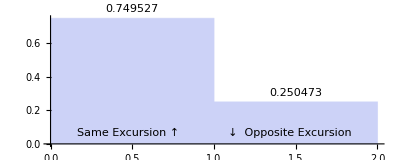

{char t,4.24772,-0.0388683, Years from,1881.,to,2013.,CC,72.8669,72.864,-0.00289191}

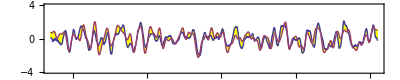

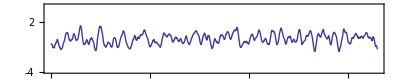

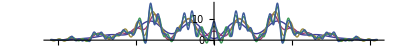

```mathematica
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 10;  WinLoFilter = 97;  Future=0;  Past=0;
R1 = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
R2 = -1.62*(MeanFilter[NINO34[[All,2]],WinHiFilter] - MeanFilter[NINO34[[All,2]],WinLoFilter]); 
100*Correlation[R1,R2]
R =(R1+R2)/2;
(* R = 0.5*(MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter]) -
   0.5*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter])
   + -1.62*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter]; *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6985; CW = 0.9731; MW := 0.1252; CF = 2.188;  
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 76;
qbo[x_] := + 0.97*( (sigmoid[x,QBOTra])*Cos[QB*x+1.2+.38*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1]-0*0.01*Sin[0.1*x-0.1] ])));     (* QBO time series *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.93*(tsi0[x+0.52]);
mw[x_] := Cos[MW*(x-1.5/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
cw[x_] := +0.63*1.4*( Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-2.9]*(1+0.6*qbo[x+1.1]);
RHS[x_]:= .32*(0.081*qbo[x+.5]-.015*cw[x+2.0])+ 0.015*mw[x]; 
Hill[x_] := 1.77*(-.59*cw[x+2.9]*(1+0.59*qbo[x+0.0])-0.26*qbo[x+0.8] ) ;
SOLN = NDSolve[{y''[x]+0.0*y'[x]+(CF+Hill[x+0.07])*y[x] == RHS[x+0.04], y'[2]==.009, y[2]==.0004}, y, {x, -250, 160}]; 
(* --------------------------- Chart ----------------------------------------------------------------------- *)
dilate[x_] := -0.22*Sin[2*Pi*(x-35)/110] ; 
(* QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.41]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}] *)
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
SOIM = Table[{YEAR+x, 1.25*(1.1*(0.46*mw[x+1.1]+0.09*cw[x+1] -0.5*Sin[CW/2*(x+6.3)] + 0.24*modtsi[x+0] + 0.18*qbo[x+0.2]) +
             First[-70*y[1*x+.75+dilate[x] ] /. SOLN] )       }, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.2, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-4,4}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,100,500,100}],{ω,-π/10,π/10},PlotRange->All,AspectRatio->0.1]
```

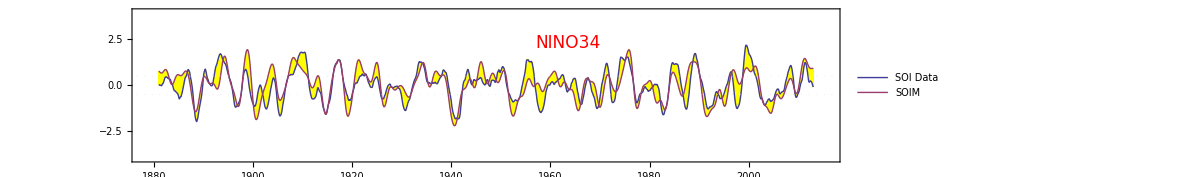

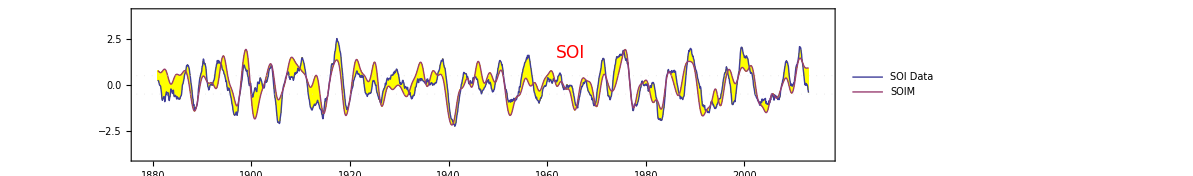

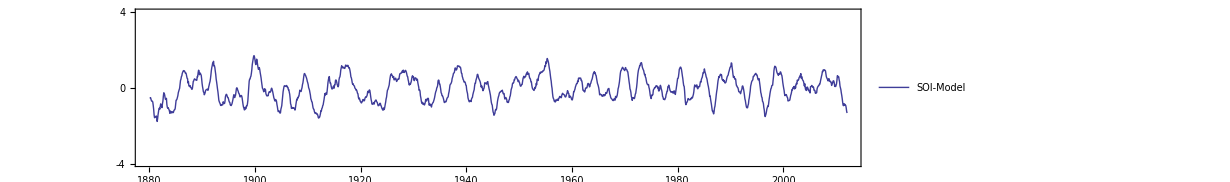

74.0695

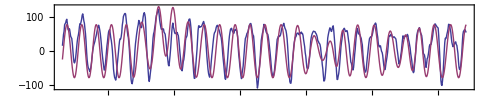

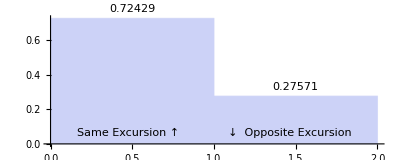

84.5438

{char t,4.24675,0.0697447, Years from,1881.,to,2013.,CC,80.7763,82.2708,1.49455}

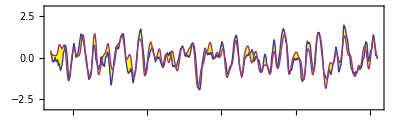

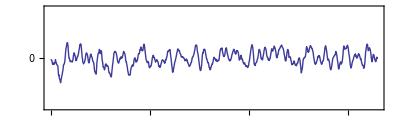

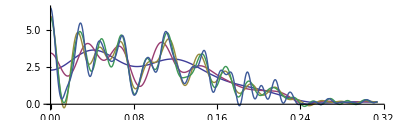

```mathematica
(* SOI Data Table from NCAR, filtered to remove seasonal noise *)
WinHiFilter = 12;  WinLoFilter = 97;  Future=0;  Past=0;
R1 = MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter] -
   1*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter]); 
R2 = -1.62*(MeanFilter[NINO34[[All,2]],WinHiFilter] - MeanFilter[NINO34[[All,2]],WinLoFilter]); 
100*Correlation[R1,R2]
R =(R1+R2)/2;
(* R = 0.5*(MeanFilter[tahiti[[All,2]],WinHiFilter] - MeanFilter[darwin[[All,2]],WinHiFilter]) -
   0.5*(MeanFilter[tahiti[[All,2]],WinLoFilter] - MeanFilter[darwin[[All,2]],WinLoFilter])
   + -1.62*MeanFilter[NINO34[[All,2]],WinHiFilter] + 1*MeanFilter[NINO34[[All,2]],WinLoFilter]; *)
STRT=12; YEAR=1880; STRTY=YEAR+STRT/12; SEP=0; LNGTH=1596; ENDY=1880+LNGTH/12; 
SOIT = Table[{YEAR+i/12, R[[i]]+0.000001+SEP},{i,STRT,LNGTH,1}];   
(* -------------------------------------------------------------------------------- *)
(* shaping functions for capturing model of TSI *)
ga2[x_,T_] := 0.12/GWI* Exp[-(x-T)^2/GWI];
sigmoid[x_, T_] := 1/(1+Exp[3*(x-T)]); 
(* constants for QBO=2.33yr, TS=10.6yr, CW=6.46yr(432day beat with 365day) and the Clarke CharFreq=4.24yr  *)
QB=2.6988; CW = 0.9731; MW := 0.1252; CF = 2.189;  DI = 8.85; (* 4.247 *)
(* closed form representations of the QBO, TSI, CW, MW data  *)
QBOTra = 76;
qbo[x_] := + 1.001*( (sigmoid[x,QBOTra])*Cos[QB*x+1.19+.38*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-20*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.24*ga2[x,97.7] -0*0.1*ga2[x,116])*x +  (*  0.6 0.24 *) (* 0.65 *)
   1.08+.4*Sin[.519*x-2.1] ])));     (* QBO time series *)
qbo[x_] := + 1.001*( (sigmoid[x,QBOTra])*Cos[QB*x+1.19+.38*Sin[.519*x-2.1] ] + (1-sigmoid[x,QBOTra])* 
     ((1-33*ga2[x,113.4]-20*ga2[x,125.0])*(+40*ga2[x,89.1]  + 
   Cos[(QB+0.62*ga2[x,84.8]-0.6*ga2[x,113.4]-0.3*ga2[x,125.2]+0.32*ga2[x,97.7] )*x +
   1.08+.4*Sin[.519*x-2.1] ])));     (* QBO time series *)
tsi0[x_] := 0.15*(1.003+0.00*x-1*1.99*(0*0.3*Tanh[(x-60)/10]+0.65*ga[x,3]+0.95*ga[x,15]+0.6*ga[x,27]+1.2*ga[x,38.5]+ga[x,49]+
      1.4*ga[x,58]+1.2*ga[x,69.3]+1.7*ga[x,79]+ga[x,90]+1.8*ga[x,101]+1.6*ga[x,111]+1.7*ga[x,121.7]+1.6*ga[x,133.5]));
tsi[x_] := 5.92*(tsi0[x+0.52]);
mw[x_] := Cos[MW*(x-1.49/MW)] ;   
(* closed form representations of the QBO, TSI, CW, MW data  *)
cw[x_] := +0.63*1.4*( Sin[CW*(x+0.92)+0.16*Sin[0.358*(x+5.5)]] ); (*.92*)
modtsi[x_] := tsi[x-2.8]*(1.1+0.3*qbo[x+1.1]);
RHS[x_]:= .33*(0.085*qbo[x+.5]-.015*cw[x+2.0])+ 0.015*mw[x] -0*0.0002*Sin[CW/2*(x+2.2)]; 
Hill[x_] := 1.76*(-.6*cw[x+2.9]*(0.99+0.63*qbo[x-0.0])-0.247*qbo[x+0.835] +0*0.045*Sin[CW/2*(x+1.7)] ) ;
Resid[x_]:= 0.49*mw[x+1.1]+0.16*cw[x+0.9]-0.35*Sin[CW/2*(x+6)]+0.18*modtsi[x+0]+0*0.18*qbo[x+0.32]-
   0.29*Sin[Sqrt[CF]*(x-1.22)]+0.18*Sin[2*Pi/DI*(x-1.7)]-0.15*Sin[2*Pi/5*(x-1.47)]-WinHiFilter*0.026*Sin[QB*x+0.22]-
   0.14*Sin[2*Pi/3.65*x-0.07]-0.08*Sin[4*Pi/DI*(x+3.91)]; 
SOLN = NDSolve[{y''[x]+(CF+Hill[x+0.066])*y[x] == RHS[x+0.036], y'[2]==.009, y[2]==.00033}, y, {x, -250, 160}]; 
dilate[x_] := -0.1*Sin[2*Pi*(x-38)/114] ; 
SOIM = Table[{YEAR+x, Sqrt[12/WinHiFilter]*1.25*(1*Resid[x]+First[-67*y[1.*x+.83+dilate[x] ] /. SOLN])}, {x,STRT/12-Past,LNGTH/12+Future, 1/12}];  
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM]; 
(* --------------------------- Chart ----------------------------------------------------------------------- 0.18*qbo[x+0.32]-0.2*Sin[2*Pi/2.33*x-0.1] *)
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False,  PlotLegends->{"NINO34+SOI\naverage","SOIM", "pure"},
            Filling->{1->{{2},Yellow}}, AspectRatio->0.3, GridLines->{None,{{-0.5,Dotted},{0.5,Dotted}} }]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];   Var = Variance[SDIF];
 ListLinePlot[SDIF,  PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.3,
FrameTicks->{{{-4, -2, 0, 2, 4}, None},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,100,500,100}],{ω,0,π/10},PlotRange->All,AspectRatio->0.3]
(*QBOM = Table[{1953.0+x, 80*qbo[73.0+x+0.41]-0},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];      
100*Correlation[QBOT,QBOM][[2,2]]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO 70 hPa", "Model"}] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.4,
   ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]   (* -0.18*Sin[2*Pi/4.29*(x-0.42)]  74.266 *)
*)
```

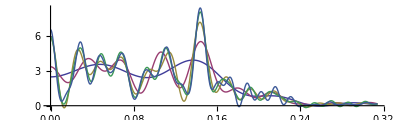

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

```mathematica
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```